```mathematica
<<"C:/users/julian/documents/github/Machine-Vision/MVTools.m"
```

```mathematica
NaturalImagePatches=Import["C:\\Users\\Julian\\Documents\\GitHub\\Machine-Vision\\Statistics\\NaturalImagePatches16x16.wdx"];
```

```mathematica
TrainingLabels=Table[RandomInteger[],{1000}];
```

```mathematica
TrainingImages=Table[
p=RandomInteger[Length[NaturalImagePatches]];
cent=Random[];
If[TrainingLabels[[t]]==1,
Table[
If[Sqrt[(x-8)^2+(y-8)^2]<=6,cent+Random[]/10.,NaturalImagePatches[[p,y,x]]],
{y,1,+16},{x,1,+16}],
NaturalImagePatches[[p]]]
,{t,1,Length[TrainingLabels]}];
```

```mathematica
Export["C:\\Users\\Julian\\Documents\\GitHub\\Machine-Vision\\NeuralNetworks\\CircleRecognition\\CircleTrainingImages.wdx",TrainingImages];
```

```mathematica
Export["C:\\Users\\Julian\\Documents\\GitHub\\Machine-Vision\\NeuralNetworks\\CircleRecognition\\CircleTrainingLabels.wdx",TrainingLabels];
```

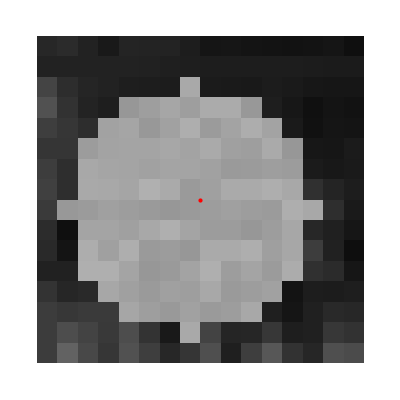

```mathematica
TrainingImages[[320]]//DispImage
```